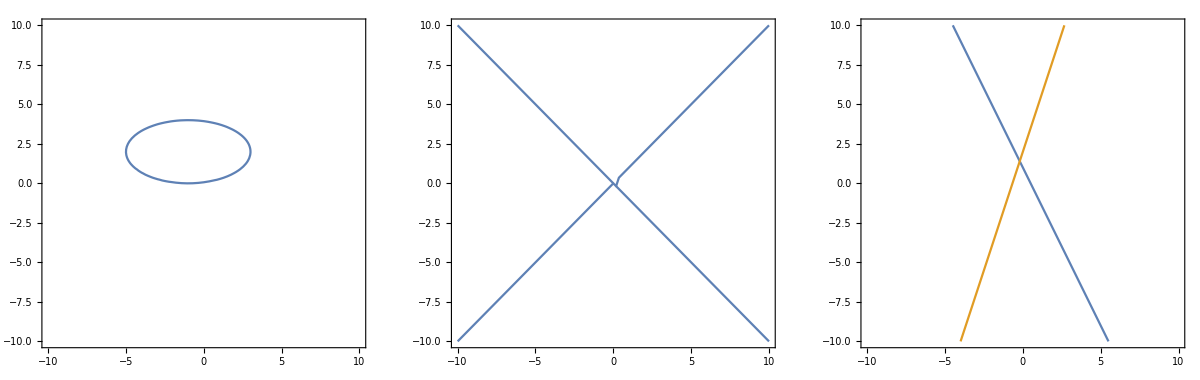

```mathematica
GraphicsGrid[{{ContourPlot[x^2 + 4y^2 + 2x - 16y +1 == 0,{x,-10,10},{y,-10,10}],ContourPlot[x^2 - y^2 == 0,{x,-10,10},{y,-10,10}], ContourPlot[{2x + y - 1 == 0,3x - y +2 == 0},{x,-10,10},{y,-10,10}]}}]
```

```mathematica
PolynomialGCD[x^3+2 x^2-x-2,x^3-2 x^2-x+2,x^3-x^2-4 x+4]
PolynomialGCD[x^4+x^2+1,x^4-x^2-2 x-1,x^3-1]
```

-1+x

1+x+x^2

```mathematica
f=x^7  y^2 + x^3  y^2 - y + 1;
p={x y^2-x,x-y^3};
{q,r} = PolynomialReduce[f,p,{x,y}, MonomialOrder -> DegreeLexicographic]
```

{{x^2+x^6,0},1+x^3+x^7-y}

```mathematica
f=x^7 y^2+x^3 y^2-y+1;
p={x-y^3,x y^2-x};
{q,r} = PolynomialReduce[f,p,{x,y, z}, MonomialOrder -> DegreeLexicographic]
```

{{0,x^2+x^6},1+x^3+x^7-y}

```mathematica
f=x^3 - x^2 y - x^2 z + x;
p={x^2 y - z,x y -1};
{q,r} = PolynomialReduce[f,p,{x,y, z}, MonomialOrder -> DegreeLexicographic]
```

{{-1,0},x+x^3-z-x^2 z}

```mathematica
f=x^3 - x^2 y - x^2 z + x;
p={x y -1, x^2 y - z};
{q,r} = PolynomialReduce[f,p,{x,y, z}, MonomialOrder -> DegreeLexicographic]
```

{{-x,0},x^3-x^2 z}

```mathematica
(* 2.4 *)
```

```mathematica
(* 17 *)
GroebnerBasis[{x^2 - y , y + x^2 - 4},{x, y}]
GroebnerBasis[{x^2 - y , x^2 - 2},{x, y}]
```

{-2+y,-2+x^2}

{-2+y,-2+x^2}

```mathematica
(* 2.6 *)

(* 10 *)
s =y z^2-x z+y;
p = {x y^2-x z+y,x y-z^2,x-y z^4};
PolynomialReduce[s,p,{x,y,z}, MonomialOrder->Lexicographic]
```

{{0,0,-z},y+y z^2-y z^5}

```mathematica
(* 2.8 *)

(* 1 *)
g = GroebnerBasis[{-x^3 +y, x^2 y- z}, {x, y}];
f = x y^3 - z^2 + y^5 - z^3;
PolynomialReduce[f, g, {x, y, z}, MonomialOrder->Lexicographic]
```

{{1,0,1,0,0},0}

```mathematica
(* 2 *)
g = GroebnerBasis[{z+2z^2,y-z,-z+x z}, {x, y}];
f = x^3 z-2y^2;
PolynomialReduce[f, g, {x, y, z}, MonomialOrder->Lexicographic]
```

{{-1,-2 y-2 z,1+x+x^2},2 z}

```mathematica
(* 3 *)
g = GroebnerBasis[{x^2+y^2+z^2-1,x^2+y^2+z^2-2 x,2x-3y-z}, {x, y}];
f = x^3 z-2y^2;
PolynomialReduce[f, g, {x, y, z}, MonomialOrder->Lexicographic]
```

{{-1,-2 y-2 z,1+x+x^2},2 z}

```mathematica
(* 6 *)
GroebnerBasis[{x-t-u,y-t^2-2 t u,z-t^3-3 t^2 u},{t,u,x,y,z}]
```

{-3 x^2 y^2+4 y^3+4 x^3 z-6 x y z+z^2,2 u y^3+x y^3-4 x^2 y z+5 y^2 z-2 u z^2-2 x z^2,-2 u y^2-x y^2+2 u x z+2 x^2 z-y z,u x y-x^2 y+2 y^2-u z-x z,2 u x^2-2 x^3-2 u y+3 x y-z,u^2-x^2+y,t+u-x}

```mathematica
(* 7 *)
GroebnerBasis[{x-t u,y-1+u,z-t-u+t u},{t,u,x,y,z}]
```

{1-2 y+x y+y^2-z+y z,-1+u+y,1+t-x-y-z}

```mathematica
(* 3.1 *)

(* 2 *)
GroebnerBasis[{x^2 + 2y^2 - 3, x^2 + x y + y^2 - 3},{y,x}]
GroebnerBasis[{x^2 + 2y^2 - 3, x^2 + x y + y^2 - 3},{x, y}]
```

{3-4 x^2+x^4,-3 x+x^3+2 y}

{-y+y^3,x y-y^2,-3+x^2+2 y^2}

```mathematica
(* 4 *)
GroebnerBasis[{x^2 + y^2 + z^2 - 4, x^2 + 2y^2 - 5, x z -1},{x,y,z}]
```

{1-3 z^2+2 z^4,-1+y^2-z^2,x-3 z+2 z^3}

```mathematica
(* 7 *)
GroebnerBasis[{t^2 + x^2 + y^2 + z^2, t^2 + 2x^2 -x y -z^2, t+ y^3 - z^3},{t, x,y,z}]
```

{5 y^4+5 y^8+y^12+13 y^2 z^2+6 y^6 z^2-10 y^5 z^3-4 y^9 z^3+9 z^4-12 y^3 z^5+5 y^2 z^6+6 y^6 z^6+6 z^8-4 y^3 z^9+z^12,-5 y^3-5 y^7-y^11+3 x z^2-7 y z^2-3 y^5 z^2+10 y^4 z^3+4 y^8 z^3+6 y^2 z^5+x z^6-3 y z^6-5 y^5 z^6+2 y^2 z^9,x y+2 y^2+y^6+3 z^2-2 y^3 z^3+z^6,x^2+y^2+y^6+z^2-2 y^3 z^3+z^6,t+y^3-z^3}

```mathematica
(* 3.2 *)
```

```mathematica
(* 2 *)
GroebnerBasis[{x y -1, x z -1}, {x,y,z}]
GroebnerBasis[{x z -1, y - z}, {x,y,z}]
```

{y-z,-1+x z}

{y-z,-1+x z}

```mathematica
(* 3.3 *)

(* 2 *)
GroebnerBasis[{x- u v , y - u^2 , z - v^2}, {u, v, x , y , z}]
```

{x^2-y z,v^2-z,-v x+u z,u x-v y,u v-x,u^2-y}